```mathematica
dclose = 4.0047514582383403;
psi50gomp = -2.026065085544674;
g0 = 0.038826552773327597;
g1 = 2.0853069797819042;

vpd = 289.81243896484375;
p = 101299.99999999999;
anet = 1.4249999523162842;
ca = 425;
LAI = 4.2606200839802524;
κL = 0.41742122142237131;
κS  = 50;
kxylemsat  = 471.1319534827615;
Η = 0.00028918089895410001;

h = 30;

x1 = 0.5;
x2 = 0.88;
ψ50= -3.5949303594944122;
ψ88= -4.5000747565338601;

ci=Log[Log[1.-x1]/Log[1.-x2]]/(Log[-ψ50]-Log[-ψ88]);
bi=-ψ50/((-Log[1.-x1])^(1./ci));
k[ψ_]:= (Exp[-(ψ/bi)^ci])
minP = ψ88*20;
maxP = 0.0;
values = Table[{ψ,k[-ψ]}, {ψ, minP, maxP, 0.01}];
θ[ψ_]:=Round[Rescale[ψ, {minP, maxP}, {1, Length@values}]]

ψS =-4.03315407512998;
ψL0 = -4.3;


β[ψL_] := Exp[-Exp[-dclose*( ψL-psi50gomp)]];
```

General::munfl: Exp[-6.36456×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.36104×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.35752×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
gs[ψL_]:= 1.6(g0 + β[ψL]*(1.0 + g1/Sqrt[vpd/p])*anet/ca);
J[ψL_]:= (
n =10;
ψH = 998 * 9.81* h/10^6/n;
Δψ= (ψS-ψL)/n;
Js = Total[Table[values[[θ[ψ]]][[2]]* Δψ - ψH, {ψ, MovingAverage[Table[ψ, {ψ, ψL,ψS, Δψ}],2]}]];
Return[Js *kxylemsat*Η/h];
)
T[ψL_]:= LAI *gs[ψL]*vpd/p
dψL[ψL_]:= (J[ψL]-T[ψL])/κL
```

General::munfl: Exp[-9.02866×10^19] is too small to represent as a normalized machine number; precision may be lost.

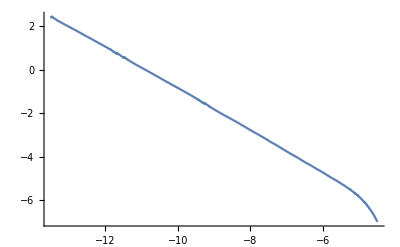

```mathematica
Plot[ψL0 +dψL[ψL]*1800-ψL,{ψL, -13.5, -4.5}]
```